```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.



```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

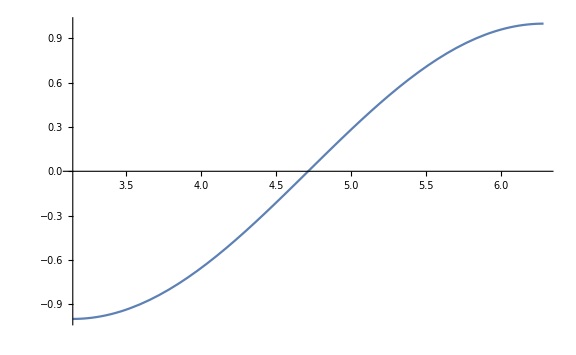

```mathematica
Plot[Cos[k],{k,Pi,2Pi},ImageSize->Large]
```

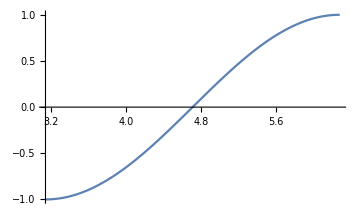

```mathematica
Show[%3,ImageSize->Medium]
```

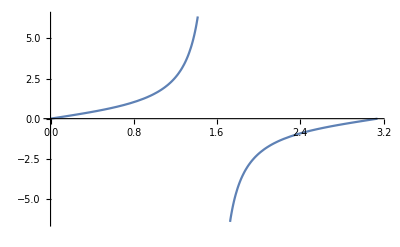

```mathematica
Plot[1/Cot[x],{x,0,Pi}]
```

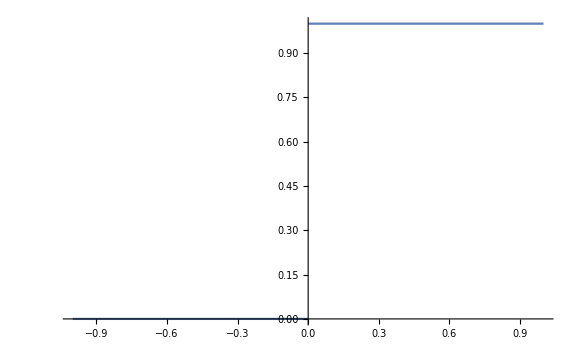

```mathematica
Plot[HeavisideTheta[K],{K,-1,1}, ImageSize->Large]
```

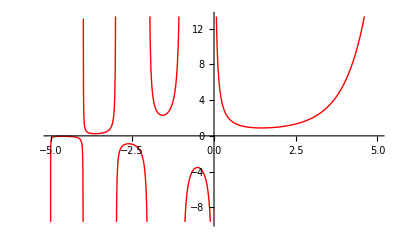

```mathematica
Plot[Gamma[x],{x,-5,5},PlotStyle->{Red,Thick}]
```

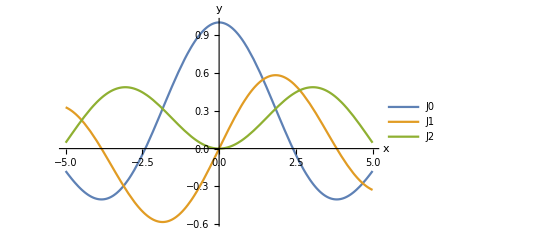

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,-5,5},AxesLabel->{"x","y"},PlotLegends->{"J0","J1","J2"}]
```

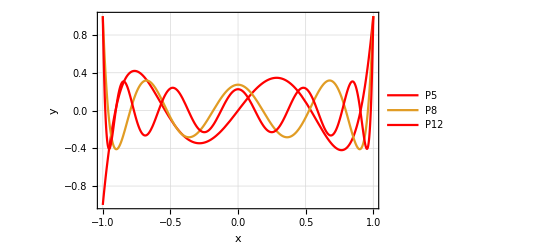

```mathematica
Plot[
{LegendreP[5,x],LegendreP[8,x],LegendreP[12,x]},
{x,-1,1},
AxesLabel->{"x","y"},
PlotLegends->{"P5","P8","P12"},
PlotStyle->{Red,Thick},
GridLines->Automatic,
Frame->True
]
```

```mathematica
GraphicsRow[
{Plot[
{LegendreP[5,x],LegendreP[8,x],LegendreP[12,x]},
{x,-1,1},
AxesLabel->{"x","y"},
PlotLabel->"Legendre Ploynomial",
PlotLegends->{"P5","P8","P12"},
PlotStyle->{Red,Thick},
ImageSize->Large,
GridLines->Automatic,
Frame->True
],
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},
{x,-5,5},
AxesLabel->{"x","y"},
PlotLabel->"BesselJ",
ImageSize->Large,
GridLines->Automatic,
PlotStyle->{Red,Thick},
Frame->True,
PlotLegends->{"J0","J1","J2"}]}
]
```

-Graphics-